```mathematica
Quit[]
```

First we need to load PolylogTools. This should ideally be the first instruction executed in a fresh kernel. In particular all other packages should be loaded afterwards to avoid shadowing of variables.

```mathematica
<<PolyLogTools`;
```

(****** PolyLogTools 1.2 ******)

Authors: Claude Duhr, Falko Dulat

Emails: claude.duhr@cern.ch, dulatf@slac.stanford.edu

PolyLogTools uses the implementation of the PSLQ algorithm by P. Bertok (http://library.wolfram.com/infocenter/MathSource/4263/)

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

In this notebook we will demonstrate how to compute the one-loop four-mass box I^4(u,v) using PolyLogTools.

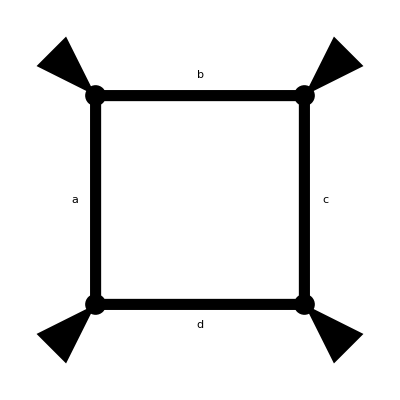

```mathematica
wedge[θ_]:=Triangle[RotationMatrix[θ].#&/@{{-0.1,-.3},{0.1,-.3},{0,0}}]
Graphics[{Thickness[.02],Line[{{{0,1},{1,1}},{{1,1},{1,0}},{{1,0},{0,0}},{{0,0},{0,1}}}],wedge[-Pi/4],Translate[wedge[-3/4 Pi],{0,1}],Disk[#,0.05]&/@{{0,0},{1,0},{0,1},{1,1}},Translate[wedge[3/4 Pi],{1,1}],Translate[wedge[1/4 Pi],{1,0}],Text[Style[a,Large],{-0.1,0.5}],Text[Style[b,Large],{0.5,1.1}],Text[Style[c,Large],{1.1,0.5}],Text[Style[d,Large],{0.5,-0.1}]}]
```

In dual coordinates we have the Feynman parametrization:
I^4(u,v)=∫d^4 k ((a,c)(b,d)Δ_6(u,v))/((k,a)(k,b)(k,c)(k,d))
In e.g. arXiV:1901.02887 it is shown how to derive the manifestly dual-conformal invariant parametrization that we will start from below.
We have the dual-conformal invariant cross-ratios:
u=((a,b)(c,d))/((a,c)9b,d)) and v=((a,d)(b,c))/((a,c)(b,d)). 
Furthermore we have the gram determinant Δ_6(u,v)=√(1-u-v)^2-4u v.
A common way to remove the explicit square root, due to the Gram determinant, is to introduce new variables that linearize the square root.
However, here we will refrain from doing so, in order to show how to deal with square roots in PolyLogTools.

```mathematica
integrand=del6/2/(α[1]u+α[2]+α[3]v)/(α[1]α[2]+α[1]α[3]+α[2]α[3])
```

del6/(2 (u α[1]+α[2]+v α[3]) (α[1] α[2]+α[1] α[3]+α[2] α[3]))

The integral is over ℙ^3, we can choose a chart by setting any one of the α_ito 1.In this case, neither choice is better than the others.
We compute the primitive w.r.t α_1.

```mathematica
prim=GIntegrate[integrand/.α[3]->1,α[1]]//Factor
```

-((del6 (-G[-α[2]/(1+α[2]),α[1]]+G[-(v+α[2])/u,α[1]]))/(2 (v+α[2]-u α[2]+v α[2]+α[2]^2)))

In order to evaluate the primitive on either boundary, we use the function ExpandPolyLogs, which implements a series expansion of the polylogarithms around zero argument and uses Mathematica’s Series[] function internally to expand potential algebraic coefficients of  the polylogarithms.

```mathematica
at0=ExpandPolyLogs[prim,{α[1],0,0}]
```

0

PolyLogTools does not support directly expanding Gs around infinity. This is however not a limitation, as we can use the core functionality of PolyLogTools, ToFibrationBasis[], to refiber the expression after inverting the variable.

```mathematica
invprim=ToFibrationBasis[prim/.α[1]->1/t,{t,α[2],u,v}]
```

(del6 (G[-1,α[2]]-G[0,t]-G[0,α[2]]+G[-1-1/α[2],t]))/(2 (v+α[2]-u α[2]+v α[2]+α[2]^2))-(del6 (-G[0,t]+G[0,u]-G[0,v]-G[-v,α[2]]+G[-u/(v+α[2]),t]))/(2 (v+α[2]-u α[2]+v α[2]+α[2]^2))

Now we have an expression that has manifestly α_1=∞ mapped to t=0 and we can expand.

```mathematica
atinf=ExpandPolyLogs[invprim,{t,0,0}]
```

(del6 G[-1,α[2]]-del6 G[0,u]+del6 G[0,v]-del6 G[0,α[2]]+del6 G[-v,α[2]])/(2 (v+α[2]-u α[2]+v α[2]+α[2]^2))

The integrand for the next iterated integral is then the primitive evaluated on the endpoints of the chosen path.

```mathematica
next=atinf-at0//Factor
```

(del6 (G[-1,α[2]]-G[0,u]+G[0,v]-G[0,α[2]]+G[-v,α[2]]))/(2 (v+α[2]-u α[2]+v α[2]+α[2]^2))

```mathematica
Collect[Denominator[next]/2,α[2],Factor]
```

v+(1-u+v) α[2]+α[2]^2

Here we see now a slight obstruction. The integration variable appears quadratically in the denominator.
Out of the box, PolylogTools does not know how to handle such cases, as GIntegrate[] relies on being able to partial fraction the integrand into terms with only linear denominator polynomials.
But we can of course simply solve the quadratic equation to factor the denominator explicitly. In doing so we identify the gram determinant Δ_6.
We should note, that it is always a good idea to mask square roots that appear in this procedure with (dummy-)variables since GIntegrate[] calls Mathematica’s Apart[] internally, which might otherwise undo the factorization.

```mathematica
Solve[Denominator[next]==0,α[2]]
```

{{α[2]→1/2 (-1+u-v-√(-4 v+(1-u+v)^2))},{α[2]→1/2 (-1+u-v+√(-4 v+(1-u+v)^2))}}

```mathematica
Denominator[next]
Solve[%==0,α[2]]/.Power[_,1/2]->del6
newDenom=Coefficient[%%,α[2],2](α[2]-(α[2]/.%[[1]]))(α[2]-(α[2]/.%[[2]]))
```

2 (v+α[2]-u α[2]+v α[2]+α[2]^2)

{{α[2]→1/2 (-1-del6+u-v)},{α[2]→1/2 (-1+del6+u-v)}}

2 (1/2 (1-del6-u+v)+α[2]) (1/2 (1+del6-u+v)+α[2])

```mathematica
FullSimplify[Denominator[next]/newDenom//.del6->Sqrt[(1-u-v)^2-4u v]]
```

1

```mathematica
factored=Numerator[next]/newDenom
```

(del6 (G[-1,α[2]]-G[0,u]+G[0,v]-G[0,α[2]]+G[-v,α[2]]))/(2 (1/2 (1-del6-u+v)+α[2]) (1/2 (1+del6-u+v)+α[2]))

Having factored the denominator and masked the root, we can continue by finding the next primitive.

```mathematica
prim=GIntegrate[factored,α[2]]
```

1/2 (G[0,u]-G[0,v]) G[1/2 (-1-del6+u-v),α[2]]+1/2 (-G[0,u]+G[0,v]) G[1/2 (-1+del6+u-v),α[2]]-1/2 G[1/2 (-1-del6+u-v),-1,α[2]]+1/2 G[1/2 (-1-del6+u-v),0,α[2]]-1/2 G[1/2 (-1-del6+u-v),-v,α[2]]+1/2 G[1/2 (-1+del6+u-v),-1,α[2]]-1/2 G[1/2 (-1+del6+u-v),0,α[2]]+1/2 G[1/2 (-1+del6+u-v),-v,α[2]]

Once again the expansion around 0 is straightforward.

```mathematica
at0=ExpandPolyLogs[prim,{α[2],0,0}]
```

0

And for ∞ we perform again the inversion.

```mathematica
invprim=prim/.α[2]->1/t;
```

Rather than calling ToFibrationBasis[] on the entire expression, we can also explicitly extract the G functions appearing using GetGs[].

```mathematica
thegs=GetGs[invprim]
```

{G[0,u],G[0,v],G[1/2 (-1-del6+u-v),1/t],G[1/2 (-1+del6+u-v),1/t],G[1/2 (-1-del6+u-v),-1,1/t],G[1/2 (-1-del6+u-v),0,1/t],G[1/2 (-1-del6+u-v),-v,1/t],G[1/2 (-1+del6+u-v),-1,1/t],G[1/2 (-1+del6+u-v),0,1/t],G[1/2 (-1+del6+u-v),-v,1/t]}

This is useful in this case, since it allows us to check the fibration results of individual polylogarithms.  In particular, we can make sure that the point we chose for the FitValue did not introduce any spurious i*π terms.

```mathematica
red=Thread[thegs->ToFibrationBasis[thegs,{t,del6,u,v},FitValue->{t->.1,del6->.12,u->.23,v->.45}]];
FreeQ[red,I]
```

True

```mathematica
atinf=ExpandPolyLogs[invprim//.Dispatch[red],{t,0,0}];
```

After evaluating the primitive on the contour, we obtain the result of the integral.

```mathematica
result=atinf-at0//GCoefficientSimplify
```

-1/2 G[-1,v] G[1-u-v,del6]+1/2 G[0,2] G[1-u-v,del6]+1/2 G[0,v] G[1-u-v,del6]-1/2 G[-1,v] G[-1+u-v,del6]+1/2 G[0,2] G[-1+u-v,del6]-1/2 G[0,u] G[-1+u-v,del6]+1/2 G[0,v] G[-1+u-v,del6]+1/2 G[-1,v] G[1+u-v,del6]-1/2 G[0,2] G[1+u-v,del6]-1/2 G[1-u-v,del6] G[1+v,u]-1/2 G[-1+u-v,del6] G[1+v,u]+1/2 G[1+u-v,del6] G[1+v,u]-1/2 G[-1,v] G[-1-u+v,del6]+1/2 G[0,2] G[-1-u+v,del6]-1/2 G[1+v,u] G[-1-u+v,del6]+1/2 G[-1,v] G[1-u+v,del6]-1/2 G[0,2] G[1-u+v,del6]+1/2 G[0,u] G[1-u+v,del6]-1/2 G[0,v] G[1-u+v,del6]+1/2 G[1+v,u] G[1-u+v,del6]+1/2 G[-1,v] G[-1+u+v,del6]-1/2 G[0,2] G[-1+u+v,del6]-1/2 G[0,v] G[-1+u+v,del6]+1/2 G[1+v,u] G[-1+u+v,del6]-1/2 G[1-u-v,1-u+v,del6]-1/2 G[-1+u-v,-1+u-v,del6]+1/2 G[1+u-v,-1+u-v,del6]-1/2 G[-1-u+v,1-u+v,del6]+1/2 G[1-u+v,1-u+v,del6]+1/2 G[-1+u+v,-1+u-v,del6]

We can perform one important check on the result here: Looking at the symbol, analyticity requires that only the letters u and v appear in the left-most slot of the symbol.

```mathematica
ComputeSymbol[result]
```

1/2 2⊗(1-del6-u-v)-1/2 2⊗(1+del6-u-v)-1/2 2⊗(1-del6+u-v)+1/2 2⊗(1+del6+u-v)-1/2 2⊗(1-del6-u+v)+1/2 2⊗(1+del6-u+v)+1/2 u⊗(1-del6-u+v)-1/2 u⊗(1+del6-u+v)+1/2 v⊗(1-del6-u-v)-1/2 v⊗(1+del6-u-v)-1/2 v⊗(1-del6-u+v)+1/2 v⊗(1+del6-u+v)+1/2 (1-del6-u+v)⊗2+1/2 (1-del6-u+v)⊗u-1/2 (1-del6-u+v)⊗(1-del6-u-v)-1/2 (1-del6-u+v)⊗(1+del6+u-v)+1/2 (1-del6-u+v)⊗(1-del6-u+v)-1/2 (1+del6-u+v)⊗2-1/2 (1+del6-u+v)⊗u+1/2 (1+del6-u+v)⊗(1+del6-u-v)+1/2 (1+del6-u+v)⊗(1-del6+u-v)-1/2 (1+del6-u+v)⊗(1+del6-u+v)

The fact that this does not seem to be the case, can be traced back to the fact that PolylogTools does not know to exploit the explicit form of del6.
We can this, by factoring the terms in the symbol.
PolylogTools provides the function FactorSymbol[] which tries to combine similar terms in a symbol and simplify the resulting products. In order for this function to work well, the coefficients of the symbol should ideally be integers (because 1/2 Log[x] → Log[Sqrt[x]]).
After factoring the terms in the symbol, we can plug in the explicit form of the root and cancel products of the root (in this case we can use FullSimplify, in general care needs to be taken so that the roots stay on the correct branches).
Re-expanding the symbol in the end yields the desired form of the symbol which shows that indeed our result for the four mass box fulfills the first entry condition.

```mathematica
ComputeSymbol[2result]
1/2SymbolFactor[%]
FullSimplify[%/.del6->Sqrt[(1-u-v)^2-4u v]]/.Power[f_,1/2]:>Power[Expand[f],1/2]
symbol=SymbolExpand[%/.Power[Evaluate[Expand[(1-u-v)^2-4 u v]],1/2]->del6]
```

2⊗(1-del6-u-v)-2⊗(1+del6-u-v)-2⊗(1-del6+u-v)+2⊗(1+del6+u-v)-2⊗(1-del6-u+v)+2⊗(1+del6-u+v)+u⊗(1-del6-u+v)-u⊗(1+del6-u+v)+v⊗(1-del6-u-v)-v⊗(1+del6-u-v)-v⊗(1-del6-u+v)+v⊗(1+del6-u+v)+(1-del6-u+v)⊗2+(1-del6-u+v)⊗u-(1-del6-u+v)⊗(1-del6-u-v)-(1-del6-u+v)⊗(1+del6+u-v)+(1-del6-u+v)⊗(1-del6-u+v)-(1+del6-u+v)⊗2-(1+del6-u+v)⊗u+(1+del6-u+v)⊗(1+del6-u-v)+(1+del6-u+v)⊗(1-del6+u-v)-(1+del6-u+v)⊗(1+del6-u+v)

1/2 (2⊗((1+del6+u-v) (1+del6-u+v) (-1+del6+u+v))/((1+del6-u-v) (-1+del6+u-v) (-1+del6-u+v))+u⊗(1-(2 del6)/(1+del6-u+v))+v⊗((1+del6-u+v) (-1+del6+u+v))/((1+del6-u-v) (-1+del6+u-v))+(1-del6-u+v)⊗(2 u (-1+del6+u-v))/((1+del6+u-v) (-1+del6+u+v))+(1+del6-u+v)⊗-((1+del6-u-v) (-1+del6-u+v))/(2 u (1+del6-u+v)))

1/2 (u⊗(1-(2 √(1-2 u+u^2-2 v-2 u v+v^2))/(1-u+v+√(1-2 u+u^2-2 v-2 u v+v^2)))+v⊗(1+u-v-√(1-2 u+u^2-2 v-2 u v+v^2))/(1+u-v+√(1-2 u+u^2-2 v-2 u v+v^2)))

1/2 u⊗(1-del6-u+v)-1/2 u⊗(1+del6-u+v)+1/2 v⊗(1-del6+u-v)-1/2 v⊗(1+del6+u-v)

We can also compare against the known literature result:

```mathematica
literature=PolyLog[2,ut]+PolyLog[2,vt]+1/2 Log[u]Log[v]-Log[ut]Log[vt]-Zeta[2]//.{ut->1/2(1-u+v+del6),vt->1/2(1+u-v+del6)}
```

-π^2/6+1/2 Log[u] Log[v]-Log[1/2 (1+del6+u-v)] Log[1/2 (1+del6-u+v)]+PolyLog[2,1/2 (1+del6+u-v)]+PolyLog[2,1/2 (1+del6-u+v)]

```mathematica
Ginsh[literature-result/.del6->Sqrt[(1-u-v)^2-4u*v],{u->0.1,v->0.23}]
```

0

A common variable transformation that removes the square root is to let {u,v}→{z zb,(1-z)(1-zb)}, where z is complex and zb=z^*.

```mathematica
PowerExpand[Simplify[result/.del6->Sqrt[(1-u-v)^2-4u*v]/.{u->z*zb,v->(1-z)(1-zb)}]];
resultzzb=ShuffleG[ToFibrationBasis[%,{z,zb}]]
```

1/2 G[0,zb] G[1,z]-1/2 G[0,z] G[1,zb]-1/2 G[0,1,z]+1/2 G[0,1,zb]+1/2 G[1,0,z]-1/2 G[1,0,zb]

As we can see, the result simplifies drastically in these variables. Looking at the symbol we see a particular simple structure:

```mathematica
SymbolFactor[ComputeSymbol[2resultzzb]]/.(-1+x_):>-a(1-x)/.a->1
```

((1-z) (1-zb))⊗zb/z+(z zb)⊗(1-z)/(1-zb)

Unitarity demands that the first entry of the symbol is in this case either u=z*zb or v=(1-z)*(1-zb). In both cases, this is the absolute value of a complex number which is positive.
We can therefore see that the function can never develop a branch cut as a function of z and zb. In other words, the result can be written as single valued polylogarithms in z.
We can verify this explicitly by projecting the result onto the holomorphic variable and acting with the single-valued map on the remainder:

```mathematica
holomorphicProjection=resultzzb/.G[0,zb]->0/.zb->0
```

-1/2 G[0,1,z]+1/2 G[1,0,z]

```mathematica
resultSv=SV[holomorphicProjection]
ShuffleG[cGToG[%]/.Conjugate[z]->zb]
%-resultzzb
```

-1/2 cG[0,1,z]+1/2 cG[1,0,z]

1/2 G[0,zb] G[1,z]-1/2 G[0,z] G[1,zb]-1/2 G[0,1,z]+1/2 G[0,1,zb]+1/2 G[1,0,z]-1/2 G[1,0,zb]

0

Polylogtools knows how to evaluate SVMPLs numerically and we can thus also compare numerically:

```mathematica
Ginsh[literature-resultSv/.del6->Sqrt[(1-u-v)^2-4u*v]/.{u->z*zb,v->(1-z)(1-zb)}/.zb->Conjugate[z],{z->.3+I 0.8}]
```

0